# 实验五 中值定理的验证

## 一.实验目的

## 二.预备知识

## 三.实验内容与要求

1. 拉格朗日中值定理：
 	若f (x) 在闭区间[a, b] 上连续， 在开区间 (a, b) 内可导则：至少在开区间 (a, b) 内存在一个点 ξ ，满足. 
  编程验证：拉格朗日中值定理 对函数 在区间[1, 3] 上的正确性。

2.  定积分 中值定理：
	 若f (x) 在闭区间[a, b] 上连续，则：至少在开区间 (a, b) 内存在一个点 ξ ，满足
编程验证：拉格朗日中值定理 对函数 在区间[1, 3] 上的正确性。

## 1. 拉格朗日中值定理

Find ξ = 2.11963 属于(a,b) 满足 f'(ξ)= (f (b) - f (a))/(b - a)

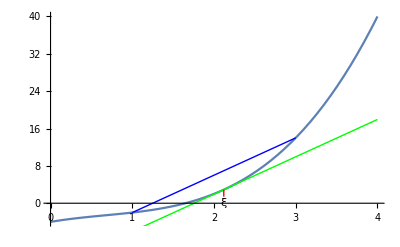

```mathematica
f[x_]:=x^3-2x^2+3x-4
a = 1;
b = 3;
Plot[{f[x],f'[x]},{x,0,4}];
t1 = Plot[f[x],{x,0,4}];
f'[x] == D[f[x],x];
d = Solve[f'[ξ]-(f[b]-f[a])/(b-a)==0, ξ];
ξ1 = d[[1]][[1]][[2]] //N;
ξ2 = d[[2]][[1]][[2]] //N;
If[1< ξ1<3,Print["Find ξ = ",ξ1,"属于(a,b) 满足 f'(ξ)= (f (b) - f (a))/(b - a) "]]
If[1< ξ2<3,Print["Find ξ = ",ξ2," 属于(a,b) 满足 f'(ξ)= (f (b) - f (a))/(b - a) "]]
t1;
t2 = Graphics[{Blue,Thick,Line[{{1,f[1]},{3,f[3]}}]}]; (*构建一条直线*)
g[x_]:=f[ξ2]+f'[ξ2](x-ξ2) (*切线方程*)
t3 = Plot[g[x],{x,0,4},PlotStyle->{Green,Thick}]; (*画出切线方程*)
t4 = Graphics[{Red,Dashed,Line[{{ξ2,f[ξ2]},{ξ2,0}}]}]; (*红色虚线*)
t5 = Graphics[Text[ξ,{ξ2,0}]];
Show[t1,t2,t3,t4,t5]
```

Find ξ = 2.15644属于(a,b) 满足 f'(ξ)= (f (b) - f (a))/(b - a)

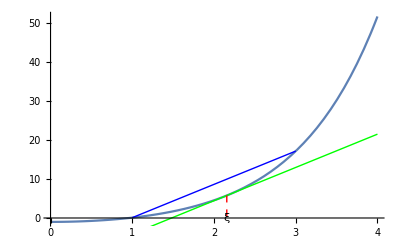

```mathematica
f[x_]:=ⅇ^x+ⅇ^-x-3
a = 1;
b = 3;
t1 = Plot[f[x],{x,0,4}];
d = FindRoot[f'[ξ]-(f[b]-f[a])/(b-a)==0,{ξ,2}];
ξ1 = d[[1]][[2]] //N;
If[1< ξ1<3,Print["Find ξ = ",ξ1,"属于(a,b) 满足 f'(ξ)= (f (b) - f (a))/(b - a) "]]
t2 = Graphics[{Blue,Thick,Line[{{1,f[1]},{3,f[3]}}]}];
g[x_]:=f[ξ1]+f'[ξ1](x-ξ1);
t3 = Plot[g[x],{x,0,4},PlotStyle->{Green,Thick}];
t4 = Graphics[{Red,Dashed,Line[{{ξ1,f[ξ1]},{ξ1,0}}]}];
t5 = Graphics[Text[ξ,{ξ1,0}]];
Show[t1,t2,t3,t4,t5]
```

## 2. 定积分中值定理

find ξ = 2.1613满足f(ξ)(∫_a^b)/(b - a)

Less::nord: 尝试使用 -0.580651-1.91645 ⅈ 进行无效的比较.

General::stop: 在本次计算中，Less::nord 的进一步输出将被抑制.

If[Complex==Real&&1<-0.580651-1.91645 ⅈ<3,Print[find ξ = ,ξ2,满足f(ξ)(∫_a^b)/(b - a)]]

Less::nord: 尝试使用 -0.580651+1.91645 ⅈ 进行无效的比较.

General::stop: 在本次计算中，Less::nord 的进一步输出将被抑制.

If[Complex==Real&&1<-0.580651+1.91645 ⅈ<3,Print[find ξ = ,ξ3,满足f(ξ)(∫_a^b)/(b - a)]]

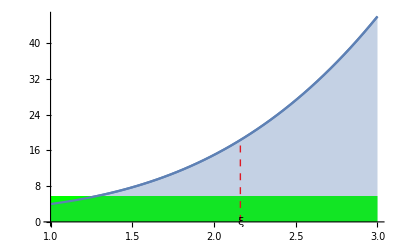

```mathematica
ff[x_]:=2x^3-2x^2+3x+1;
a = 1;
b = 3;
tt1 = Plot[ff[x],{x,0,4}];
dd = Solve[ff[ξ]-(∫_a^b ff[x]ⅆx)/(b-a)==0,ξ] //N;
ξ1 = dd[[1]][[1]][[2]] //N;
ξ2 = dd[[2]][[1]][[2]] //N;
ξ3 = dd[[3]][[1]][[2]] //N;
If[Head[ξ1]==Real&&1<ξ1<3,Print["find ξ = ",ξ1,"满足f(ξ)(∫_a^b)/(b - a)"]]
If[Head[ξ2]==Real&&1<ξ2<3,Print["find ξ = ",ξ2,"满足f(ξ)(∫_a^b)/(b - a)"]]
If[Head[ξ3]==Real&&1<ξ3<3,Print["find ξ = ",ξ3,"满足f(ξ)(∫_a^b)/(b - a)"]]
tt1 =  Plot[ff[x],{x,a,b},Filling->Bottom];
tt2 = Graphics[{Green,Rectangle[{a,0},{b,f[ξ1]}],Red,Dashed,Line[{{ξ1,0},{ξ1,ff[ξ1]}}]}];
tt3 = Graphics[Text[ξ,{ξ1,0}]];
Show[tt1,tt2,tt1,tt3]
```

By Yu Ling. Blog:The Rain Pavilion.